```mathematica
d=2;
eLRF[energy_,Mx_,My_]:=-((d-1)*energy)/2+1/2*√((d+1)^2*energy^2-4.0*d*(Mx^2+My^2));
Temp[e_]:=(π*e)^(1/3);(*temperature in 2d*)
gammasquared[energy_,Mx_,My_]:=(energy+eLRF[energy,Mx,My]/d)/((d+1)*eLRF[energy,Mx,My]/d);
entropy[energy_,Mx_,My_]:=((d+1)/d*eLRF[energy,Mx,My])/Temp[eLRF[energy,Mx,My]]*√gammasquared[energy,Mx,My];
```

```mathematica
Intx[energy_?NumericQ,Mx_?NumericQ]:=NIntegrate[Exp[entropy[energy,Mx,My]],{My,-√(energy^2-Mx^2),√(energy^2-Mx^2)}];
normalization1=NIntegrate[Intx[5,Mx],{Mx,-5,5}];
```

```mathematica
plotE5=Table[Flatten[{Mx,Intx[5,Mx]/normalization1}],{Mx,-5.0,5.0,0.01}];
```

```mathematica
Export["E5.txt",plotE5,"Table"]
```

E5.txt

```mathematica
plotE2=Table[Flatten[{Mx,Intx[2,Mx]/normalization[2]}],{Mx,-2.0,2.0,1}];
```

$Aborted

```mathematica
Export["E2.txt",plotE2,"Table"]
```

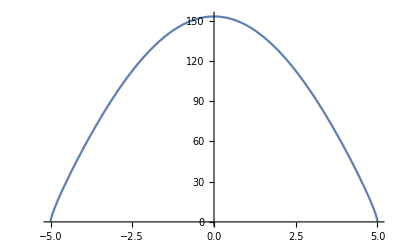

```mathematica
Plot[Intx[5,Mx],{Mx,-5,5}]
```

```mathematica
Integrate[Exp[-x^2/(2k)],{x,-∞,∞}]
```

ConditionalExpression[√k √(2 π), Re[k]>0]

```mathematica
N[(1+1/2)*985*Temp[985]]
```

21530.6

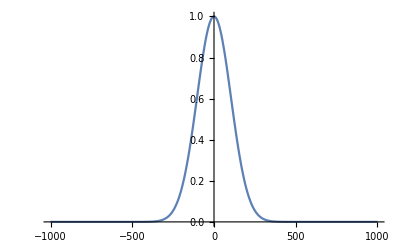

```mathematica
Plot[Exp[-x^2/21530],{x,-1000,1000},PlotRange->All]
```

```mathematica
N[972.2/(√(2π*3/2*972.2*Temp[972.2]))]
```

2.6664

```mathematica
N[(2*3/2*972.2*Temp[972.2])/972.2^2]
```

0.0447714

```mathematica
N[972.2/(√(2π*3/2*972.2*Temp[972.2]*2))]
```

1.88543

```mathematica
N[(2*3/2*972.2*Temp[972.2]*2)/972.2^2]
```

0.0895428

```mathematica
N[1000/Sqrt[2 π*3/2*1000*Temp[1000]]]
N[(2*3/2*1000*Temp[1000])/1000^2]
```

2.69157

0.0439378